```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_Tiingo_LTC";
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
F2NIG[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,μ2_?NumericQ,δ_?NumericQ,δ1_?NumericQ,δ2_?NumericQ]:=
NIntegrate[FNIG[x-z,α,β,μ1,δ1] FNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

Make density out of cdf

-Graphics-

```mathematica
f2NIG[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,μ2_?NumericQ,δ_?NumericQ,δ1_?NumericQ,δ2_?NumericQ]:=
NIntegrate[fNIG[x-z,α,β,μ1,δ1] fNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

```mathematica
Timing[F2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{5.17385,0.547637}

```mathematica
Timing[f2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{0.01653,0.3921}

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},n=Length[s];If[Length[x]==0,N[Length[Select[s,#1≤x&]]/(n+1)],Table[N[Length[Select[s,#1≤x⟦k⟧&]]/(n+1)],{k,1,Length[x]}]]]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | ltc Price | log return future | log return ltc
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 210.069 | 0.0212907 | 0.0373946
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 202.358 | -0.0904653 | -0.375913
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 294.698 | -0.0196938 | 0.0455332
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 281.581 | -0.131645 | -0.139733
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 323.809 | 0.03685 | 0.0859344
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 297.144 | -0.119603 | -0.177521
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 354.866 | -0.042369 | -0.0471009
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 371.98 | 0.018947 | 0.0151204
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 366.398 | -0.0359909 | 0.0584074)

```mathematica
data[[1,7]]
```

log return ltc

```mathematica
data[[1,6]]
```

log return future

```mathematica
tmp=Import[NotebookDirectory[] <> "data_ltc/" <> ToString[kk] <> "_parameters.csv"]
```

(2021-05-20
2.37993
-1.4806
0.89046)

```mathematica
α=tmp[[2,1]]; 
β=tmp[[3,1]];
δ=tmp[[4,1]];
```

```mathematica
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
```

Attempt to determine LL from simulated data turns out to be very noisy

```mathematica
tmp=Import[NotebookDirectory[] <> "data_ltc/" <> ToString[kk] <> "_simulation.csv"];
```

```mathematica
tmp[[1;;10]]
```

(0.152177 | 0.0771185
0.00957981 | 0.00897982
0.774465 | 0.628387
0.773045 | 0.563969
0.967141 | 0.946881
0.844243 | 0.9832
0.741445 | 0.52267
0.843983 | 0.694806
0.468491 | 0.576688
0.9967 | 0.99956)

```mathematica
Dimensions[tmp]
```

{50000,2}

```mathematica
uv=tmp;
skd=SmoothKernelDistribution[uv];
```

-Graphics-

copula density

```mathematica
c2NIG[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ]:=Module[{x,y},
x=NIGInv[u,α,β];
y=NIGInv[v,α,β];
f2NIG[x,y,α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ] / (NIGPDF[x,α,β] NIGPDF[y,α,β])
]
```

```mathematica
Timing[c2NIG[0.5,0.1,5,0,0.2]]
```

{0.083431,0.998887}

-Graphics-

-Graphics-

```mathematica
c2NIG[#[[1]],#[[2]], α, β,δ]&/@({u[[1;;5]],v[[1;;5]]}ᵀ)
```

{2.01787,2.2616,0.198026,5.71386,2.04948}

```mathematica
PDF[skd,#]& /@ ({u[[1;;5]], v[[1;;5]]}ᵀ)
```

{1.90797,3.02082,0.193842,3.30686,2.05032}

```mathematica
CNIG[u_,v_,α_,β_,δ_]:=F2NIG[NIGInv[u,α,β],NIGInv[v,α,β],α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ]
```

```mathematica
CNIG[#[[1]],#[[2]], α, β,δ]&/@({u[[1;;5]],v[[1;;5]]}ᵀ)
```

{0.61607,0.00271136,0.195414,0.0075868,0.801204}

```mathematica
CDF[skd,#]& /@ ({u[[1;;5]], v[[1;;5]]}ᵀ)
```

{0.613809,0.00758831,0.195292,0.00847527,0.797456}

```mathematica
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)]
```

125.192

```mathematica
%/Length[data]
```

0.415921

```mathematica
Timing[Total[Log[c2NIG[#[[1]],#[[2]], α, β,δ]]&/@({u,v}ᵀ)]]
```

{17.1666,155.965}

```mathematica
%/Length[data]
```

{0.0570318,0.518155}

```mathematica
tLL={};
mLL={};
For[kk=0, kk<=111, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
tmp=Import[NotebookDirectory[] <> "data_ltc/" <> ToString[kk] <> "_parameters.csv"];
α=tmp[[2,1]]; 
β=tmp[[3,1]];
δ=tmp[[4,1]];
ll=Total[Log[c2NIG[#[[1]],#[[2]], α, β,δ]]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLL, ll];
AppendTo[mLL,mll];
]
```

```mathematica
(*tLLnew={};
mLLnew={};
For[kk=0, kk<=111, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
uv=Import[NotebookDirectory[] <> "data_xrp/" <> ToString[kk] <> "_simulation.csv"];
skd=SmoothKernelDistribution[uv];
ll=
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLnew, ll];
AppendTo[mLLnew,mll];
]*)
```

```mathematica
tLL
```

{155.965,157.618,153.116,168.776,171.75,170.917,174.258,171.067,175.484,169.246,180.001,184.573,185.123,188.373,178.041,190.447,194.512,179.481,177.548,161.568,180.952,183.681,176.632,172.091,169.116,180.472,170.263,167.484,179.83,173.981,163.196,144.139,167.747,165.759,171.34,171.629,172.504,137.555,132.475,145.252,146.892,151.061,129.208,133.569,143.146,127.44,123.971,125.346,144.763,145.086,143.802,135.744,137.261,138.112,139.823,136.444,133.905,134.415,133.562,131.255,128.133,122.473,122.773,134.423,136.572,134.628,136.651,136.296,128.597,132.169,130.116,118.767,117.098,123.435,129.274,127.989,129.081,131.627,137.451,138.781,138.891,136.592,130.318,134.656,134.183,138.929,144.863,140.949,139.988,141.722,144.945,151.066,148.836,153.212,158.297,153.255,163.97,174.301,176.549,182.564,182.662,188.35,163.637,157.787,158.922,178.831,192.772,187.142,186.342,198.785,189.485,189.711}

```mathematica
mLL
```

{0.518155,0.523648,0.50869,0.560717,0.570598,0.56783,0.578931,0.568329,0.583005,0.56228,0.59801,0.613201,0.615026,0.625823,0.591498,0.632715,0.64622,0.596283,0.589861,0.536771,0.60117,0.610235,0.586816,0.571732,0.561846,0.599574,0.565659,0.556426,0.597443,0.57801,0.54218,0.478867,0.5573,0.550696,0.569235,0.570197,0.573103,0.456993,0.440115,0.482566,0.488013,0.501863,0.429263,0.443752,0.475569,0.423388,0.411863,0.416432,0.48094,0.482013,0.477749,0.450976,0.456017,0.458843,0.464528,0.453303,0.444867,0.446561,0.443727,0.436064,0.425691,0.406887,0.407884,0.446587,0.453726,0.447269,0.453991,0.45281,0.427233,0.439101,0.432278,0.394574,0.389029,0.410083,0.429481,0.425214,0.428839,0.437299,0.456649,0.461065,0.461431,0.453794,0.432949,0.447362,0.445789,0.461557,0.481274,0.468269,0.465078,0.470836,0.481544,0.501881,0.494472,0.50901,0.525903,0.509153,0.544749,0.579074,0.586543,0.606524,0.606852,0.625749,0.543645,0.524208,0.527981,0.594122,0.640437,0.621736,0.619075,0.660414,0.629518,0.63027}

```mathematica
Export[NotebookDirectory[] <> "data_ltc/LL_NIG_ltc.csv", Prepend[{Range[0,111],tLL, mLL}ᵀ, {"", "LL", "mean LL"}]]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/data_ltc/LL_NIG_ltc.csv

```mathematica
(*Export[NotebookDirectory[] <> "data_xrp/LL_NIG_new.csv", Prepend[{Range[0,87],tLLnew, mLLnew}ᵀ, {"", "LL", "mean LL"}]]*)
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/data/LL_NIG_new.csv

Gaussian copula

```mathematica
LLg[x_]:=Log[PDF[BinormalDistribution[{0,0}, {1,1}, ρ], x]]-Total[Log[PDF[NormalDistribution[],#]&/@x]]
```

```mathematica
ρ=0.9907220113152815;
ρ=0.9891018086831789;
```

```mathematica
tLLg={};
mLLg={};
For[kk=1, kk<=1, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
(* tmp=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv"]; *)
(* look at parameters.json *)
ll=Total[LLg[{InverseCDF[NormalDistribution[],#[[1]]],InverseCDF[NormalDistribution[],#[[2]]]}]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLg, ll];
AppendTo[mLLg,mll];
]
```

```mathematica
tLLg
```

{365.689}

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Z=RandomVariate[NormalDistribution[],{100000,2}];
```

```mathematica
X=Z[[;;,1]];
Y=ρ Z[[;;,1]] + Sqrt[1-ρ^2] Z[[;;,2]];
```

```mathematica
U=hatF[X];
V=hatF[Y];
```

```mathematica
skd=SmoothKernelDistribution[{U,V}ᵀ];
ll=
Total[Log[PDF[skd,#]]& /@ ({u, v}ᵀ)];
```

```mathematica
ll
```

382.909

Clayton copula

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
```

```mathematica
LLc[u_]:=Log[PDF[𝒟, u]]-Total[Log[#&/@u]]
```

```mathematica
c=40;
```

```mathematica
tLLc={};
mLLc={};
For[kk=18, kk<=18, kk++,
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
(* tmp=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv"]; *)
(* look at parameters.json *)
ll=Total[LLc[{#[[1]],#[[2]]}]&/@({u,v}ᵀ)];
mll=ll/Length[data];
AppendTo[tLLc, ll];
AppendTo[mLLc,mll];
]
```

```mathematica
tLLc
```

{548.926}

```mathematica
mLLc
```

{1.82367}

```mathematica
Quantile[𝒟, {0.5, 0.5}]
```

Quantile[CopulaDistribution[{Clayton,1/40},{UniformDistribution[{0,1}],UniformDistribution[{0,1}]}],{0.5,0.5}]

-Graphics-

```mathematica
ClaytonCDF[u_,v_]:=(u^-c+v^-c-1)^(-1/c)
```

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
```

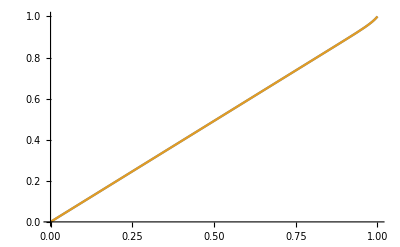

```mathematica
Plot[{CDF[𝒟, {u,u}],ClaytonCDF[u,u]}, {u,0,1}]
```

```mathematica
Simplify[ClaytonCDF[q,q]/q]
```

1/((2/q^40-1)^(1/40) q)

```mathematica
Simplify[CDF[𝒟,{q,q}]/q, Assumptions->0<q<1]
```

1/((2-q^40)^(1/40))

```mathematica
QD[q_?NumericQ]:=
If[0<q≤0.5, CDF[𝒟,{q,q}]/q,(1-2q+ CDF[𝒟, {q,q}])/(1-q)]
```

```mathematica
QD2[q_?NumericQ]:=
If[0<q≤0.5, ClaytonCDF[q,q]/q,(1-2q+ ClaytonCDF[q,q])/(1-q)]
```

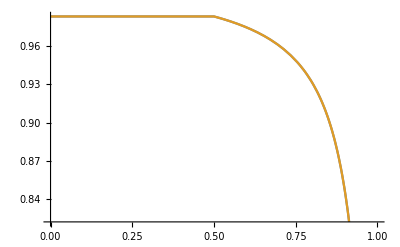

```mathematica
Plot[{QD[q],QD2[q]}, {q,0,1}]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
kk=18;
```

```mathematica
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
u=hatF[data[[2;;,7]]];
v=hatF[data[[2;;,6]]];
```

```mathematica
Clear[c, QD,𝒟]
```

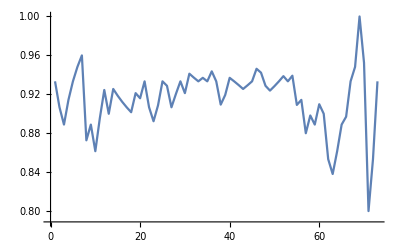

```mathematica
ListPlot[Table[QDemp[q, u, v], {q,0.05,0.95, 0.0125}],Joined->True]
```

```mathematica
𝒟=CopulaDistribution[{"Clayton",1/c},{UniformDistribution[],UniformDistribution[]}];
QD[q_]:=
If[0<q≤0.5, CDF[𝒟,{q,q}]/q,(1-2q+ CDF[𝒟, {q,q}])/(1-q)]
```

```mathematica
target=Table[QDemp[q, u, v], {q,{0.05,0.1, 0.9, 0.95}}];
AppendTo[target, KendallTau[u,v]];
target
```

{0.933333,0.933333,1.,0.933333,0.884563}

```mathematica
f= Table[QD[q], {q,{0.05,0.1, 0.9, 0.95}}];
AppendTo[f, c/(c+2)]; (* Kendall's tau *)
Sqrt[Total[(target-f)^2]]
```

√((0.933333-20. (2 0.05^-c-1)^(-1/c))^2+(0.933333-10. (2 0.1^-c-1)^(-1/c))^2+(1.-10. ((2 0.9^-c-1)^(-1/c)-0.8))^2+(0.933333-20. ((2 0.95^-c-1)^(-1/c)-0.9))^2+(0.884563-c/(c+2))^2)

```mathematica
NMinimize[{Sqrt[Total[(target-f)^2]], c>0}, c]
```

{0.141561,{c→181.081}}

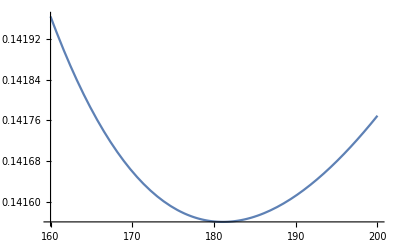

```mathematica
Plot[Sqrt[Total[(target-f)^2]], {c,160,200}]
```